```mathematica
Assuming[{r∈Reals,r>0,x∈Reals},Integrate[p/((p^2+f)(p^2+Conjugate[f]))Exp[ⅈ p r Cos[x]],{p,0,∞}]]
```

ConditionalExpression[1/(2 (f-Conjugate[f]))√π (-MeijerG[{{0},{}},{{0,0},{1/2}},1/4 f r^2 Cos[x]^2]+MeijerG[{{0},{}},{{0,0},{1/2}},1/4 r^2 Conjugate[f] Cos[x]^2]-ⅈ (ⅇ^(-√f r Abs[Cos[x]])-ⅇ^(-r Abs[Cos[x]] √Conjugate[f])) √π Sign[Cos[x]]),Im[f]≠0||(Re[f]≥0&&Re[√f]>0&&Re[√Conjugate[f]]>0)]

```mathematica
Πpar[θ_,u_,mD_]:=mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))])
```

```mathematica
Block[{u=0.2,mD=0.2,r=5/0.197},NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])(Sinh[√Πpar[x,u,mD] r Cos[x]]SinhIntegral[√Πpar[x,u,mD] r Cos[x]]-Cosh[√Πpar[x,u,mD] r Cos[x]]CoshIntegral[√Πpar[x,u,mD] r Cos[x]]-Sinh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]),{x,0,π/2}]]
```

-0.0448051+8.83544×10^-15 ⅈ

```mathematica
Block[{u=0.2,mD=0.2,r=5/0.197},(2π)/(2π)^3 NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))1/(2 (Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]]))√π (-MeijerG[{{0},{}},{{0,0},{1/2}},1/4 Πpar[x,u,mD] r^2 Cos[x]^2]+MeijerG[{{0},{}},{{0,0},{1/2}},1/4 r^2 Conjugate[Πpar[x,u,mD]] Cos[x]^2]-ⅈ (ⅇ^(-√Πpar[x,u,mD] r Abs[Cos[x]])-ⅇ^(-r Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]])) √π Sign[Cos[x]]),{x,0,π}]]
```

0.0567463-6.60874×10^-17 ⅈ

```mathematica
-0.204541211846094/0.25905447116949304
```

-0.789568

```mathematica
-0.044805059639633577/0.05674627094886522
```

-0.789568

```mathematica
D[(Sinh[√f r Cos[x]]SinhIntegral[√f r Cos[x]]-Cosh[√f r Cos[x]]CoshIntegral[√f r Cos[x]]-Sinh[√Conjugate[f] r Cos[x]]SinhIntegral[√Conjugate[f] r Cos[x]]+Cosh[√Conjugate[f] r Cos[x]]CoshIntegral[√Conjugate[f] r Cos[x]]),{r,2}]+2/r D[(Sinh[√f r Cos[x]]SinhIntegral[√f r Cos[x]]-Cosh[√f r Cos[x]]CoshIntegral[√f r Cos[x]]-Sinh[√Conjugate[f] r Cos[x]]SinhIntegral[√Conjugate[f] r Cos[x]]+Cosh[√Conjugate[f] r Cos[x]]CoshIntegral[√Conjugate[f] r Cos[x]]),r]//FullSimplify
```

1/r Cos[x] (-CoshIntegral[√f r Cos[x]] (f r Cos[x] Cosh[√f r Cos[x]]+2 √f Sinh[√f r Cos[x]])+√f (2 Cosh[√f r Cos[x]]+√f r Cos[x] Sinh[√f r Cos[x]]) SinhIntegral[√f r Cos[x]]+2 √Conjugate[f] (CoshIntegral[r √Conjugate[f] Cos[x]] Sinh[r √Conjugate[f] Cos[x]]-Cosh[r √Conjugate[f] Cos[x]] SinhIntegral[r √Conjugate[f] Cos[x]])+r Conjugate[f] Cos[x] (Cosh[r √Conjugate[f] Cos[x]] CoshIntegral[r √Conjugate[f] Cos[x]]-Sinh[r √Conjugate[f] Cos[x]] SinhIntegral[r √Conjugate[f] Cos[x]]))

```mathematica
ϵImp[r_,mD_,u_,T_]:=Re[1/(2π)T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])1/r Cos[x] (2 √Conjugate[Πpar[x,mD,u]] (CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]] Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+r Conjugate[Πpar[x,mD,u]] Cos[x] (Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+√Πpar[x,mD,u] (-CoshIntegral[r Cos[x] √Πpar[x,mD,u]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,mD,u]] √Πpar[x,mD,u]+2 Sinh[r Cos[x] √Πpar[x,mD,u]])+(2 Cosh[r Cos[x] √Πpar[x,mD,u]]+r Cos[x] √Πpar[x,mD,u] Sinh[r Cos[x] √Πpar[x,mD,u]]) SinhIntegral[r Cos[x] √Πpar[x,mD,u]])),{x,0,π/2},WorkingPrecision->20]];
```

```mathematica
ϵImp[1/(197/1000),2/10,2/10,1]
```

0.0018804102916700699702

```mathematica
Assuming[{r∈Reals,r>0,x∈Reals},Integrate[p^3/((p^2+f)(p^2+Conjugate[f]))Exp[ⅈ p r Cos[x]],{p,0,∞}]]
```

ConditionalExpression[1/(2 (f-Conjugate[f]))ⅈ (ⅈ f √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 f r^2 Cos[x]^2]+f π Sign[Cos[x]] (Cosh[√f r Abs[Cos[x]]]-Sinh[√f r Abs[Cos[x]]])+Conjugate[f] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[f] Cos[x]^2]+π Sign[Cos[x]] (-Cosh[r Abs[Cos[x]] √Conjugate[f]]+Sinh[r Abs[Cos[x]] √Conjugate[f]]))),Im[f]≠0||(Re[f]≥0&&Re[√f]>0&&Re[√Conjugate[f]]>0)]

```mathematica
Block[{u=2/10,mD=2/10,r=1/(197/1000),T=1},(2π)/(2π)^3 NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))(π mD^2 T)/(2 (Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]]))ⅈ (ⅈ Πpar[x,u,mD] √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 Πpar[x,u,mD] r^2 Cos[x]^2]+Πpar[x,u,mD] π Sign[Cos[x]] (Cosh[√Πpar[x,u,mD] r Abs[Cos[x]]]-Sinh[√Πpar[x,u,mD] r Abs[Cos[x]]])+Conjugate[Πpar[x,u,mD]] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[x,u,mD]] Cos[x]^2]+π Sign[Cos[x]] (-Cosh[r Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]]]+Sinh[r Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]]]))),{x,0,π}]]
```

0.00195491+1.86422×10^-17 ⅈ

```mathematica
ImϵRreg[r_,mD1_,u1_,T1_,Δ1_]:=Block[{mD=mD1,T=T1,u=u1,Δ=Δ1,temp,inter},temp=Join[ParallelTable[{p,NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π}]},{p,10^-10,10,1/1000}],ParallelTable[{p,NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π}]},{p,101/10,200,1/10}]];
inter=Interpolation[temp];
Return[-(2 π^2 T mD^2)/(2π)^3 NIntegrate[inter[x],{x,0,200}]]]
```

```mathematica
ImϵRreg[1,2/10,2/10,1,6/10]//AbsoluteTiming
```

{44.1944,-0.00726519}

```mathematica
ImϵRregr[r_,mD1_,u1_,T1_,Δ1_]
```

```mathematica
Integrate[Integrate[r^2 Exp[ⅈ p r Cos[x]],r],r]//FullSimplify
```

-(ⅇ^(ⅈ p r Cos[x]) (-6+p r Cos[x] (4 ⅈ+p r Cos[x])) Sec[x]^4)/p^4

```mathematica
Limit[-(ⅇ^(ⅈ p r Cos[x]) (-6+p r Cos[x] (4 ⅈ+p r Cos[x])) Sec[x]^4)/p^4,r->0]
```

(6 Sec[x]^4)/p^4

```mathematica
Block[{u=2/10,mD=2/10,Δ=6/10,r=1,x=π/3},NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{p,0,∞}]]//AbsoluteTiming
```

{0.036581,0.691626+1.07717 ⅈ}

```mathematica
Block[{u=2/10,mD=2/10,Δ=6/10,r=1},NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π},{p,0,∞}]]//AbsoluteTiming
```

$Aborted

```mathematica
Block[{u=2/10,mD=2/10,Δ=6/10,r=1},temp=Join[ParallelTable[{p,NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π}]},{p,10^-10,10,1/1000}],ParallelTable[{p,NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))p^4/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])√(p^2+Δ^2))Exp[ⅈ p r Cos[x]],{x,0,π}]},{p,101/10,200,1/10}]];]//AbsoluteTiming
```

{43.3581,Null}

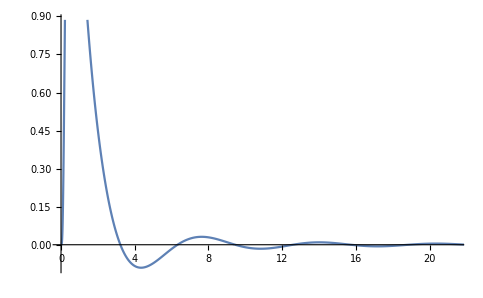

```mathematica
ListPlot[temp,Joined->True]
```

```mathematica
temp1=Interpolation[temp];
```

```mathematica
NIntegrate[temp1[x],{x,0,200}]
```

2.28243